```mathematica
LegendreP[0,0,x]
```

1

```mathematica
LegendreP[0,-1,x]
```

(√(1-x))/(√(1+x))

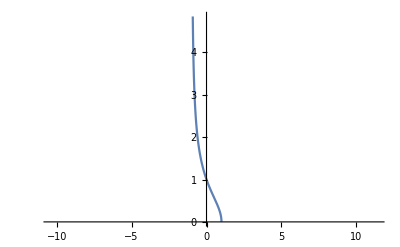

```mathematica
Plot[(√(1-x))/(√(1+x)),{x,-10.42,11.42}]
```

```mathematica
LegendreP[1,0,x]
```

x

```mathematica
LegendreP[1,1,x]
```

-√(1-x^2)

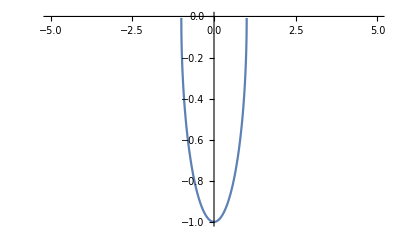

```mathematica
Plot[-√(1-x^2),{x,-5,5}]
```

```mathematica
LegendreP[1,-1,x]
```

```mathematica
(√(1-x^2))/2
plot[LegendreP[1,-1,x],{x,-5,5}]
```

(√(1-x^2))/2

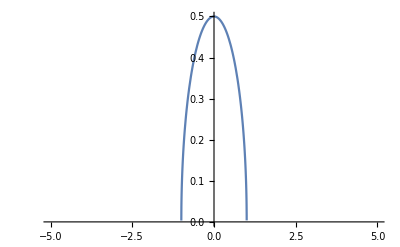

```mathematica
Plot[(√(1-x^2))/2,{x,-5,5}]
```

```mathematica
LegendreP[1,2,x]
```

0

```mathematica
LegendreP[2,0,x]
```

1/2 (-1+3 x^2)

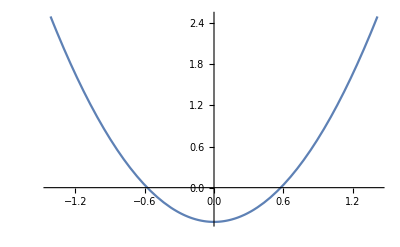

```mathematica
Plot[1/2 (-1+3 x^2),{x,-1.4142135623730954,1.4142135623730954}]
```

```mathematica
LegendreP[2,-1,x]
```

1/2 x √(1-x^2)

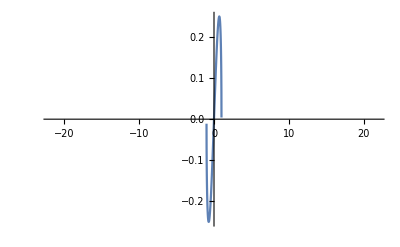

```mathematica
Plot[1/2 x √(1-x^2),{x,-21.84,21.84}]
```

```mathematica
LegendreP[2,-2,x]
```

1/8 (1-x^2)

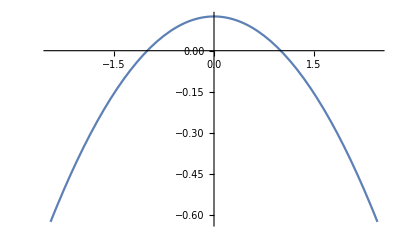

```mathematica
Plot[1/8 (1-x^2),{x,-2.449489742783178,2.449489742783178}]
```

```mathematica
LegendreP[2,1,x]
```

-3 x √(1-x^2)

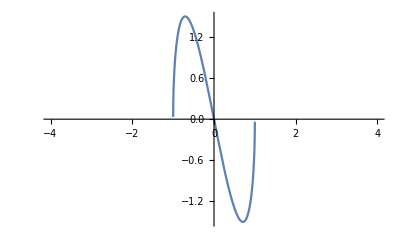

```mathematica
-3 x √(1-x^2)
Plot[LegendreP[2,1,x],{x,-4,4}]
```

```mathematica
LegendreP[2,2,x]
```

-3 (-1+x^2)

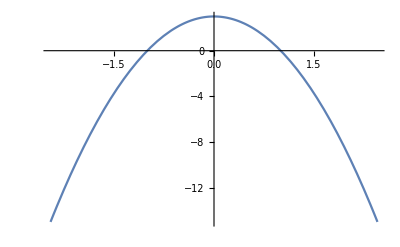

```mathematica
Plot[-3 (-1+x^2),{x,-2.449489742783178,2.449489742783178}]
```

```mathematica
LegendreP[3,0,cos(theta)]
```

1/2 (-3 cos theta+5 cos^3 theta^3)

```mathematica
Plot3D[1/2 (-3 cos theta+5 cos^3 theta^3),{cos,-1.7774221366067522,1.7671683161877687},{theta,-1.7681205780942073,1.7764698747003131}]
```

-Graphics3D-

```mathematica
Manipulate[Plot[1/2 (-3 cos t+5 cos^3 t^3),{t,-8,8}],{cos,-8,8}]
```

```mathematica
LegendreP[20,19,x]
```

-319830986772877770815625 x (1-x^2)^(19/2)

```mathematica
Plot[LegendreP[20,19,x],{x,-1,1}]
```

-Graphics-

```mathematica
LegendreP[2,2,x]
```

-3 (-1+x^2)

```mathematica
Plot[-3 (-1+x^2),{x,-2.449489742783178,2.449489742783178}]
```

-Graphics-

```mathematica
Plot[cos(x),{x,0,2.95}]
```

-Graphics-

```mathematica
LegendreP[2,2,cos[x]]
```

-3 (-1+cos[x]^2)

```mathematica
Simplify[-3 (-1+cos[x]^2)]
```

3-3 cos[x]^2

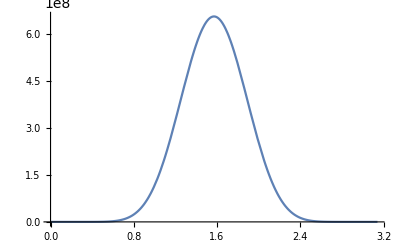

```mathematica
Plot[LegendreP[10,10,Cos[x]],{x,0, Pi}]
```

```mathematica
LegendreP[2,2,Cos[x],{x,{0.19634954631328583,0.58904863893985748,0.98174773156642914,1.3744468241930008,1.7671459168195724,2.15984500944614412.5525441020727158,2.9452431946992874}}]
```

LegendreP::ltype: Legendre type Cos[x] is expected to be 1, 2, or 3.

General::stop: Further output of LegendreP::ltype will be suppressed during this calculation.

```mathematica
Flatten[%14]
```

{LegendreP[2,2,Cos[x],x],LegendreP[2,2,Cos[x],0.19635],LegendreP[2,2,Cos[x],0.589049],LegendreP[2,2,Cos[x],0.981748],LegendreP[2,2,Cos[x],1.37445],LegendreP[2,2,Cos[x],1.76715],LegendreP[2,2,Cos[x],1.19341],LegendreP[2,2,Cos[x],2.94524]}

```mathematica
LegendreP[2,2,Cos[2.9452431946992874]]
```

0.114181

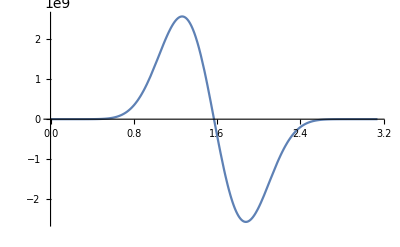

```mathematica
Plot[LegendreP[11,10,Cos[x]],{x,0,Pi}]
```

```mathematica
LegendreP[2,3,x]
```

0

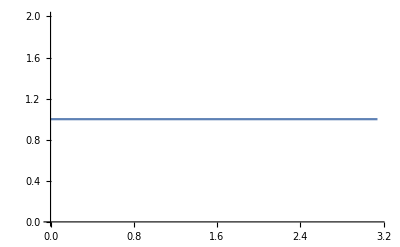

```mathematica
Plot[LegendreP[0,0,Cos[x]],{x,0,Pi}]
```

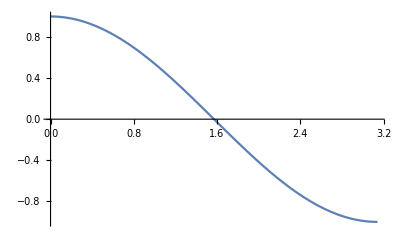

```mathematica
Plot[LegendreP[1,0,Cos[x]],{x,0,Pi}]
```

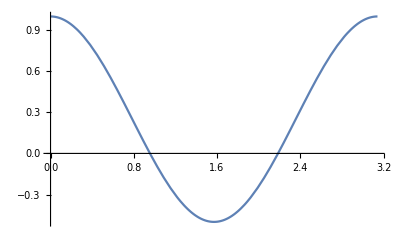

```mathematica
Plot[LegendreP[2,0,Cos[x]],{x,0,Pi}]
```

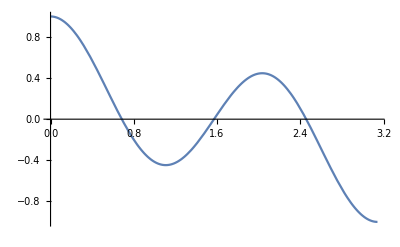

```mathematica
Plot[LegendreP[3,0,Cos[x]],{x,0,Pi}]
```

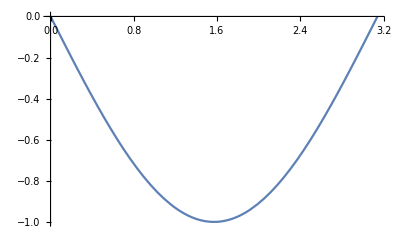

```mathematica
Plot[LegendreP[1,1,Cos[x]],{x,0,Pi}]
```

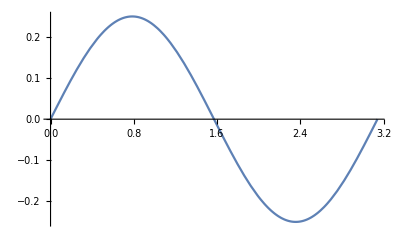

```mathematica
Plot[LegendreP[2,-1,Cos[x]],{x,0,Pi}]
```

```mathematica
LegendreP[2,1,Cos[x]]
```

-3 Cos[x] √(1-Cos[x]^2)

```mathematica
LegendreP[2,-1,Cos[x]]
```

1/2 Cos[x] √(1-Cos[x]^2)

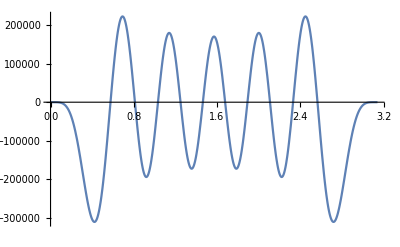

```mathematica
Plot[LegendreP[15,5,Cos[x]],{x,0,Pi}]
```

```mathematica
LegendreP[5,2,Cos[x]]
```

-105 Cos[x] (1-Cos[x]^2)^(3/2)

```mathematica
Simplify[-105 Cos[x] (1-Cos[x]^2)^(3/2)]
```

-105 Cos[x] (Sin[x]^2)^(3/2)

```mathematica
Simplify[105/2 √(1-Cos[x]^2) (-1+Cos[x]^2) (-1+9 Cos[x]^2)]
```

-105/2 (-1+9 Cos[x]^2) (Sin[x]^2)^(3/2)

```mathematica
Simplify[-105/2 (-1+Cos[x]^2) (-Cos[x]+3 Cos[x]^3)]
```

105/8 (5 Cos[x]+3 Cos[3 x]) Sin[x]^2

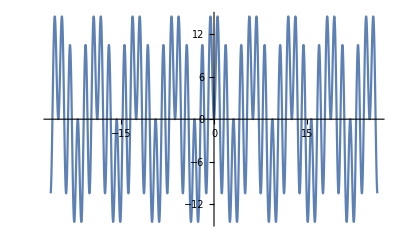

```mathematica
Plot[105/8 (5 Cos[x]+3 Cos[3 x]) Sin[x]^2,{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
Simplify[-3003/256 (-1+Cos[x]^2) (-3+225 Cos[x]^2-2550 Cos[x]^4+9690 Cos[x]^6-14535 Cos[x]^8+7429 Cos[x]^10)]
```

3003/256 (-3+225 Cos[x]^2-2550 Cos[x]^4+9690 Cos[x]^6-14535 Cos[x]^8+7429 Cos[x]^10) Sin[x]^2

```mathematica
Simplify[-2297295/16 √(1-Cos[x]^2) (-1+Cos[x]^2)^2 (-5 Cos[x]+95 Cos[x]^3-399 Cos[x]^5+437 Cos[x]^7)]
```

-2297295/16 Cos[x] (-5+95 Cos[x]^2-399 Cos[x]^4+437 Cos[x]^6) Sin[x]^4 √(Sin[x]^2)

```mathematica
Simplify[-15 (1-Cos[x]^2)^(3/2)]
```

-15 (Sin[x]^2)^(3/2)

```mathematica
Simplify[-3/2 √(1-Cos[x]^2) (-1+5 Cos[x]^2)]
```

-3/2 (-1+5 Cos[x]^2) √(Sin[x]^2)

```mathematica
Simplify[-15 (1-Cos[x]^2)^(3/2)]
```

-15 (Sin[x]^2)^(3/2)

```mathematica
Simplify[-15 Cos[x] (-1+Cos[x]^2)]
```

15 Cos[x] Sin[x]^2

```mathematica
Simplify[-3 Cos[x] √(1-Cos[x]^2)]
```

-3 Cos[x] √(Sin[x]^2)

```mathematica
Simplify[-√(1-Cos[x]^2)]
```

-√(Sin[x]^2)

```mathematica
LegendreP[7,4,Cos[x]]
```

3465/2 (-1+Cos[x]^2)^2 (-3 Cos[x]+13 Cos[x]^3)

```mathematica
Simplify[3465/2 (-1+Cos[x]^2)^2 (-3 Cos[x]+13 Cos[x]^3)]
```

3465/8 (27 Cos[x]+13 Cos[3 x]) Sin[x]^4

```mathematica
3465/2 (-1+Cos[x]^2)^2 (-3 Cos[x]+13 Cos[x]^3)
```

3465/2 (-1+Cos[x]^2)^2 (-3 Cos[x]+13 Cos[x]^3)

```mathematica
Simplify[3465/2 (-1+Cos[x]^2)^2 (-3 Cos[x]+13 Cos[x]^3)]
```

3465/8 (27 Cos[x]+13 Cos[3 x]) Sin[x]^4

```mathematica
Simplify[3465/2 (-1+Cos[x]^2)^2 (-3 Cos[x]+13 Cos[x]^3)]
```

3465/8 (27 Cos[x]+13 Cos[3 x]) Sin[x]^4

```mathematica
Simplify[3465/2 (-1+Cos[x]^2)^2 (-3 Cos[x]+13 Cos[x]^3)]
```

3465/8 (27 Cos[x]+13 Cos[3 x]) Sin[x]^4

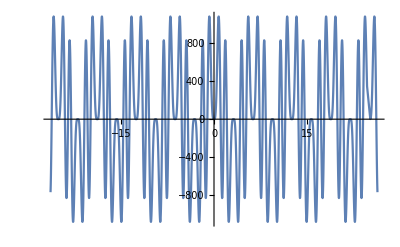

```mathematica
Plot[3465/8 (27 Cos[x]+13 Cos[3 x]) Sin[x]^4,{x,-26.389378290154262,26.389378290154262}]
```

```mathematica
Simplify[105/2 √(1-Cos[x]^2) (-1+Cos[x]^2) (-1+9 Cos[x]^2)]
```

-105/2 (-1+9 Cos[x]^2) (Sin[x]^2)^(3/2)

```mathematica
Simplify[-105/2 (-1+Cos[x]^2) (-Cos[x]+3 Cos[x]^3)]
```

105/8 (5 Cos[x]+3 Cos[3 x]) Sin[x]^2

```mathematica
LegendreP[7,4,Cos[x]]
```

3465/2 (-1+Cos[x]^2)^2 (-3 Cos[x]+13 Cos[x]^3)

```mathematica
Simplify[3465/2 (-1+Cos[x]^2)^2 (-3 Cos[x]+13 Cos[x]^3)]
```

3465/8 (27 Cos[x]+13 Cos[3 x]) Sin[x]^4

```mathematica
LegendreP[3,2,Cos[x]]
```

-15 Cos[x] (-1+Cos[x]^2)

```mathematica
Simplify[-15 Cos[x] (-1+Cos[x]^2)]
```

15 Cos[x] Sin[x]^2

```mathematica
7/7/17

-0.94104427185448725*LegendreP[2,0,Cos[x]]+4.7047456656960058*LegendreP[0,0,Cos[x]]
```

4.70475-0.470522 (-1+3 Cos[x]^2)

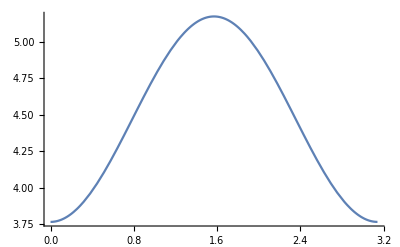

```mathematica
Plot[4.704745665696006-0.4705221359272436 (-1+3 Cos[x]^2),{x,0,Pi}]
```

```mathematica
LegendreP[2,0,Cos[x]]+LegendreP[0,0,Cos[x]]
```

1+1/2 (-1+3 Cos[x]^2)

```mathematica
Simplify[1+1/2 (-1+3 Cos[x]^2)]
```

1/4 (5+3 Cos[2 x])

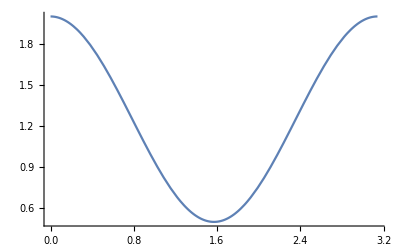

```mathematica
Plot[1/4 (5+3 Cos[2 x]),{x,0,Pi}]
```

```mathematica
Simplify[1/2 (-1+3 Cos[x]^2)]
```

1/4 (1+3 Cos[2 x])

```mathematica
Plot[1/4 (1+3 Cos[2 x]),{x,0,Pi}]
```

-Graphics-

```mathematica
9/7/17
Damn the poly nomial were upside down. huh.
```

```mathematica
LegendreP[0,0,Cos[x]]
```

1

```mathematica
0.091941531955606462*LegendreP[0,0,Cos[x]]+-0.041191930379795010*LegendreP[2,0,Cos[x]]
```

0.0919415-0.020596 (-1+3 Cos[x]^2)

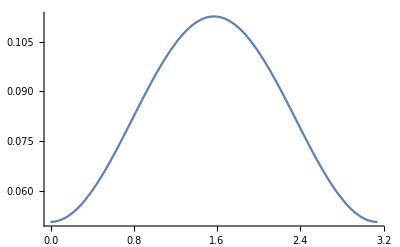

```mathematica
Plot[0.09194153195560646-0.020595965189897505 (-1+3 Cos[x]^2),{x,0,Pi}]
```

```mathematica
Equal density

See the coefficient ratio.(LinguisticAssistant)
(the above one in ~2x but this one is 4x)
```

```mathematica
1.4142135219890375*LegendreP[0,0,Cos[x]]+-0.39528469902341262*LegendreP[2,0,Cos[x]]
```

1.41421-0.197642 (-1+3 Cos[x]^2)

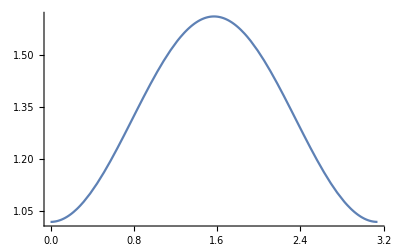

```mathematica
Plot[1.4142135219890375-0.1976423495117063 (-1+3 Cos[x]^2),{x,0,Pi}]
```

```mathematica
LegendreP[0,0,Cos[x]]
```

```mathematica
Plot[1,{x,0,Pi}]
```

-Graphics-

```mathematica
LegendreP[2,0,Cos[x]]
```

1/2 (-1+3 Cos[x]^2)

```mathematica
Simplify[1/2 (-1+3 Cos[x]^2)]
```

1/4 (1+3 Cos[2 x])

```mathematica
Plot[1/2 (-1+3 Cos[x]^2),{x,0,Pi}]
```

-Graphics-

```mathematica
1.4142135219890375*LegendreP[0,0,Cos[x]]+-0.39528469902341262*LegendreP[2,0,Cos[x]]+
-0.066291259707238259*LegendreP[4,0,Cos[x]]+
-0.024897556583290108*LegendreP[6,0,Cos[x]]
```

1.41421-0.197642 (-1+3 Cos[x]^2)-0.00828641 (3-30 Cos[x]^2+35 Cos[x]^4)-0.0015561 (-5+105 Cos[x]^2-315 Cos[x]^4+231 Cos[x]^6)

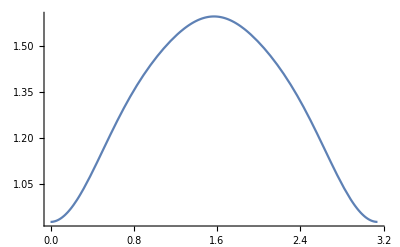

```mathematica
Plot[1.4142135219890375-0.1976423495117063 (-1+3 Cos[x]^2)-0.008286407463404782 (3-30 Cos[x]^2+35 Cos[x]^4)-0.0015560972864556318 (-5+105 Cos[x]^2-315 Cos[x]^4+231 Cos[x]^6),{x,0,Pi}]
```

```mathematica
12/7/17
```

```mathematica
LegendreP[15,6,Cos[x]]
```

-218243025/128 (-1+Cos[x]^2)^3 (21 Cos[x]-644 Cos[x]^3+4830 Cos[x]^5-12420 Cos[x]^7+10005 Cos[x]^9)

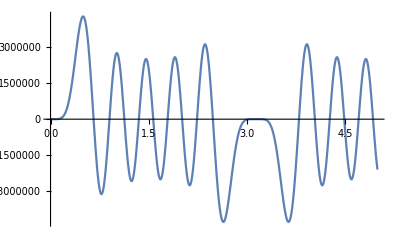

```mathematica
Plot[-218243025/128 (-1+Cos[x]^2)^3 (21 Cos[x]-644 Cos[x]^3+4830 Cos[x]^5-12420 Cos[x]^7+10005 Cos[x]^9),{x,0,5}]
```